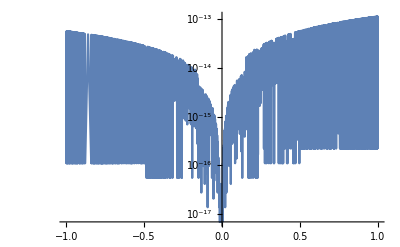

```mathematica
f[x_,ϵ_]=DSolveValue[{ϵ y''[x]+x y'[x]-y[x]==0,y[-1]==1,y[1]==2},y[x],x];
fi[x_,ϵ_]=ϵ^(1/2)(-x/ϵ^(1/2)+3/(√(2π))(ⅇ^((-(x/ϵ^(1/2))^2)/2)+x/ϵ^(1/2)∫_(-∞)^(x/ϵ^(1/2)) ⅇ^(-t^2/2)ⅆt));
LogPlot[{Abs[f[x,0.001]-fi[x,0.001]]},{x,-1,1}]
```

```mathematica
fi[1,.01]//FullSimplify
```

2.

```mathematica
RealAbs[f[x,ϵ]]//FullSimplify
```

$Aborted

```mathematica
DSolveValue[{y''[ξ]+ξ y'[ξ]==0},y[ξ],ξ]
```

C[2]+√(π/2) C[1] Erf[ξ/(√2)]

```mathematica
DSolveValue[
{s'[t]==0,
c'[t]==s[t]-(κ+s[t])c[t],
s[0]==1,
c[0]==0},{s[t],c[t]},t]//FullSimplify
```

{1,(1-ⅇ^(-t (1+κ)))/(1+κ)}

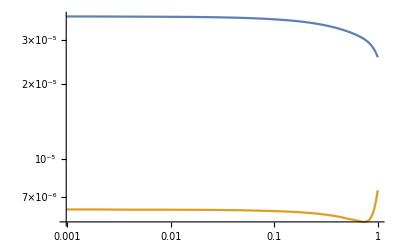

```mathematica
Module[{μ,κ,ϵ,sc,cc,st,ct},
μ=1/2;
κ=1;
ϵ=0.0001;
sc[t_]=κ ProductLog[1/κ ⅇ^(-t+μ/κ t+1/κ)];
cc[t_]=-1/(κ+1)ⅇ^(-(κ+1)t/ϵ)+(κ ProductLog[1/κ ⅇ^(-t+μ/κ t+1/κ)])/(κ+κ ProductLog[1/κ ⅇ^(-t+μ/κ t+1/κ)]);
{st[t_],ct[t_]}=NDSolveValue[
{s'[t]==-s[t]+(μ+s[t])c[t],
ϵ c'[t]==s[t]-(κ+s[t])c[t],
s[0]==1,
c[0]==0},{s[t],c[t]},{t,0,0.5}];
LogLogPlot[{Abs[sc[t]-st[t]],Abs[cc[t]-ct[t]]},{t,0,1}]]
```

```mathematica
∫_(-∞)^x ⅇ^(-t^2/2)ⅆt
```

√(π/2) (1+Erf[x/(√2)])

```mathematica
DSolveValue[
{y0''[ζ]+ζ y0'[ζ]-y0[ζ]==0},
y0[ζ],ζ]
Asymptotic[DSolveValue[
{y0''[ζ]+ζ y0'[ζ]-y0[ζ]==0},
y0[ζ],ζ]//FullSimplify,{ζ,-∞,1}]
```

ζ C[1]-1/2 ⅇ^(-ζ^2/2) C[2] (2+ⅇ^(ζ^2/2) √(2 π) ζ Erf[ζ/(√2)])

ζ C[1]+√(π/2) ζ C[2]

```mathematica
Solve[
{ζ C[1]-√(π/2) ζ C[2]==2ζ,ζ C[1]+√(π/2) ζ C[2]==-ζ},
{C[1],C[2]}]
```

{{C[1]→1/2,C[2]→-3/(√(2 π))}}

```mathematica
lim_(x->-∞) Erf[x]
```

-1

```mathematica
Asymptotic[1/2 x+3/(√(2π))(ⅇ^(-x^2/2)+x √(π/2) (1+Erf[x/(√2)])),x->∞]
```

(7 x)/2

```mathematica
Asymptotic[C[1]x-C[2](ⅇ^(-x^2/2)+x∫_(-∞)^x ⅇ^(-t^2/2)ⅆt),x->∞]
```

x C[1]-√(2 π) x C[2]